## Part 1 - Defining the Variables

First, we start off the defining the gravitational constant, G, the masses of the star, planet, and moon, and their respective distance from their orbital parents. We’ll use SI units for now but also set G=1 for simplicity. Later on, however, we’ll use a more realistic gravitational constant. The masses of the star, planet, and moon, respectively, are m1, m2, and m3 and their respective orbital distances from their orbital parents are r1, r2, and r3 (the star’s orbital distance is 0 because it’s the most massive body in the system).

```mathematica
G=100

m1=50
m2=0.0001
m3=0.000002

r1i={0,0}
r2i={50,0}
r3i={0.1,0}
```

100

50

0.0001

2.×10^-6

{0,0}

{50,0}

{0.1,0}

## Part 2 - Defining the Functions and Diff. Equations

Now let’s define the differential equations based on both Newtonian mechanics and Kepler’s laws of planetary motion.

```mathematica
r1[t_]:={x1[t],y1[t]}
r2[t_]:={x2[t],y2[t]}
r3[t_]:={x3[t],y3[t]}

r12[t_]:=r2[t]-r1[t]
r13[t_]:=r3[t]-r1[t]

r21[t_]:=r1[t]-r2[t]
r23[t_]:=r3[t]-r2[t]

r31[t_]:=r1[t]-r3[t]
r32[t_]:=r2[t]-r3[t]

acc1[t_]:={G*m2*Normalize[r12[t]][[1]]/(Norm[r12[t]])^2,G*m2*Normalize[r12[t]][[2]]/(Norm[r12[t]])^2}+{G*m3*Normalize[r13[t]][[1]]/(Norm[r13[t]])^2,G*m3*Normalize[r13[t]][[2]]/(Norm[r13[t]])^2}
acc2[t_]:={G*m1*Normalize[r21[t]][[1]]/(Norm[r21[t]])^2,G*m1*Normalize[r21[t]][[2]]/(Norm[r21[t]])^2}+{G*m3*Normalize[r23[t]][[1]]/(Norm[r23[t]])^2,G*m3*Normalize[r23[t]][[2]]/(Norm[r23[t]])^2}
acc3[t_]:={G*m1*Normalize[r31[t]][[1]]/(Norm[r31[t]])^2,G*m1*Normalize[r31[t]][[2]]/(Norm[r31[t]])^2}+{G*m2*Normalize[r32[t]][[1]]/(Norm[r32[t]])^2,G*m2*Normalize[r32[t]][[2]]/(Norm[r32[t]])^2}
```

## Part 3 - Setting Up the Initial Acc. and Velocities

We’ll use the concepts of tangential velocity and centripetal acceleration to find the initial velocities needed to keep them in circular orbits and the initial accelerations that make them go in orbit in the first place. The acceleration functions defined above represent the second time derivatives of the position functions of each celestial body.

```mathematica
acc1i={0,0};
acc2i={G*m1*Normalize[r2i][[1]]/Norm[r2i]^2,G*m1*Normalize[r2i][[2]]/Norm[r2i]^2};
acc3i={G*m2*Normalize[r3i][[1]]/Norm[r3i]^2,G*m2*Normalize[r3i][[2]]/Norm[r3i]^2};

v1i={0,0};
v2i={0,Sqrt[Norm[r2i]*Norm[acc2i]]};
v3i={0,-Sqrt[Norm[r3i]*Norm[acc3i]]}+v2i;

v1i//MatrixForm
v2i//MatrixForm
v3i//MatrixForm
```

(0
0)

(0
10)

(0
9.68377)

## Part 4 - Solving the Differential Equation

Now we’ll set the initial conditions and get ready to solve these differential equations.

```mathematica
solution=NDSolve[{x1''[t]==acc1[t][[1]],y1''[t]==acc1[t][[2]],x2''[t]==acc2[t][[1]],y2''[t]==acc2[t][[2]],x3''[t]==acc3[t][[1]],y3''[t]==acc3[t][[2]],x1[0]==r1i[[1]],y1[0]==r1i[[2]],x2[0]==r2i[[1]],y2[0]==r2i[[2]],x3[0]==r2i[[1]]+r3i[[1]],y3[0]==r2i[[2]]+r3i[[2]],x1'[0]==v1i[[1]],y1'[0]==v1i[[2]],x2'[0]==v2i[[1]],y2'[0]==v2i[[2]],x3'[0]==v3i[[1]],y3'[0]==v3i[[2]]},{x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]},{t,0,100}];

x1sol=x1[t]/.solution[[1]];
y1sol=y1[t]/.solution[[1]];

x2sol=x2[t]/.solution[[1]];
y2sol=y2[t]/.solution[[1]];

x3sol=x3[t]/.solution[[1]];
y3sol=y3[t]/.solution[[1]];
```

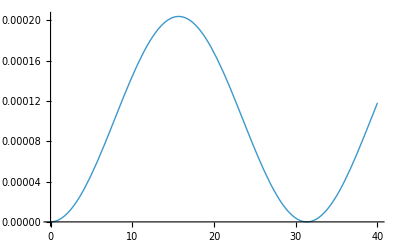

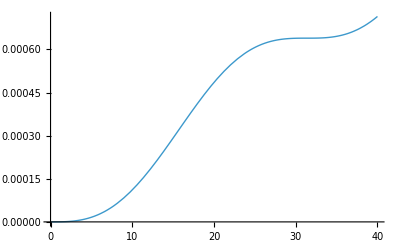

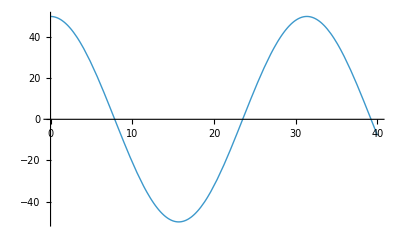

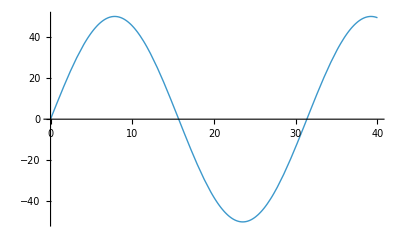

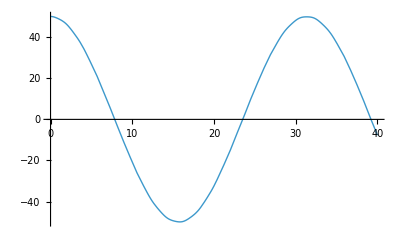

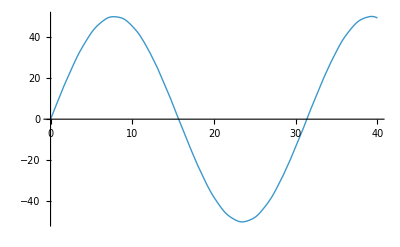

```mathematica
Plot[x1sol,{t,0,40},PlotStyle->Thick,PlotRange->All]
Plot[y1sol,{t,0,40},PlotStyle->Thick,PlotRange->All]

Plot[x2sol,{t,0,40},PlotStyle->Thick,PlotRange->All]
Plot[y2sol,{t,0,40},PlotStyle->Thick,PlotRange->All]

Plot[x3sol,{t,0,40},PlotStyle->Thick,PlotRange->All]
Plot[y3sol,{t,0,40},PlotStyle->Thick,PlotRange->All]
```

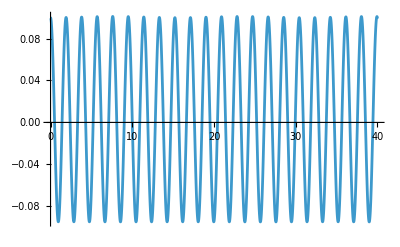

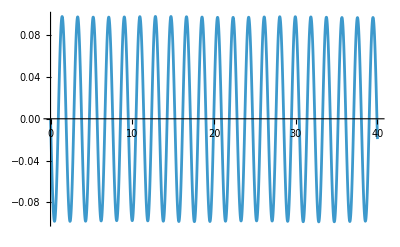

```mathematica
Plot[x3sol-x2sol,{t,0,40},PlotRange->All]
Plot[y3sol-y2sol,{t,0,40},PlotRange->All]
```